```mathematica
Sum[Binomial[2n-1,2m-1]*(L-2-2*(2m-1)),{m,1,n}]
```

-4^(-1+n) (1-L+2 n)

```mathematica
Block[{n=1},Sum[Binomial[2n-1,2m-1]*(L-2-2*(2m-1)),{m,1,n}]]
```

-4+L

```mathematica
Block[{n=1},-4^(-1+n) (1-L+2 n)]
```

-3+L

```mathematica
Block[{n=1},Sum[Binomial[2n-1,2m-1]*(L-2-2*(2m-1)),{m,1,n}]-(-4^(-1+n) (1-L+2 n))]//Expand
```

-1

```mathematica
Block[{n=1,m={1}},Binomial[2n-1,2m-1]*(L-2-2*(2m-1))]
```

{-4+L}

```mathematica
3 (-4+L)+-8+L//Expand
```

-20+4 L

```mathematica
Block[{n=2,},Table[Binomial[2n-1,2m-1]*(L-2-2*(2m-1)),{m,1,n}]]
```

{3 (-4+L),-8+L}

```mathematica
???
```

```mathematica
Sum[Binomial[2n,2m]*(L-2-2*(2m)),{m,0,n}]//FullSimplify
```

2^(-1+2 n) (L-2 (1+n))

```mathematica
Block[{n=1},Sum[Binomial[2n,2m]*(L-2-2*(2m)),{m,0,n}]]
```

-8+2 L

```mathematica
Block[{n=1},2^(-1+2 n) (L-2 (1+n))]//Expand
```

-8+2 L

```mathematica
Sum[2^((k-1)*(2n-1)+1)*Sum[Binomial[2n-1,2m-1]*(L-2-2*(2m-1)),{m,1,n}],{n,1,L/2}]+Sum[2^((k-1)*(2n)+1)*Sum[Binomial[2n,2m]*(L-2-2*(2m)),{m,0,n}],{n,1,L/2-1}]//FullSimplify
```

(-2^(k L) (-2+2^k)+2^k (-3+2^(1+k))-2^k (-1+2^k) L)/((-1+2^k)^2)

```mathematica
Sum[2^((k-1)*(2n-1)+1)*Sum[Binomial[2n-1,2m-1]*(L-2-2*(2m-1)),{m,1,n}],{n,1,L/2}]+Sum[2^((k-1)*(2n)+1)*Sum[Binomial[2n,2m]*(L-2-2*(2m)),{m,0,n}],{n,1,L/2-1}]//FullSimplify
```

(-2^(k L) (-2+2^k)+2^k (-3+2^(1+k))-2^k (-1+2^k) L)/((-1+2^k)^2)

```mathematica
op[k_,L_]:=(1-2^k)/(1-2^(k L))*(1+(1/L)*Sum[2^((k-1)F+1)*Sum[Binomial[F,i]*(L-2-2i),{i,F,0,-2}],{F,1,L-1}])
```

```mathematica
op[k_,L_]:=Sum[2^((k-1)F+1)*Sum[Binomial[F,i]*(L-2-2i),{i,F,0,-2}],{F,1,L-1}]
```

```mathematica
op2[k_,L_]:=(1-2^k)/(1-2^(k L))*(1+(1/L)*(-3 2^(1+k)+2^(1+3 k)+2^(k L)+2^(k (2+L))+3 2^(1+k+k L)-2^(1+k (3+L))-3 4^k+16^k-2^k (-1+2^k) (1+2^k) (2+2^k) L)/(2 (-1+4^k)^2))
```

```mathematica
op2[k_,L_]:=(-2^(k L) (-2+2^k)+2^k (-3+2^(1+k))-2^k (-1+2^k) L)/((-1+2^k)^2)
```

```mathematica
op[1,#]&/@{2,4,6,8,10,12,14,16}
```

{-1/3,-1/15,-1/63,-1/255,-1/1023,-1/4095,-1/16383,-1/65535}

```mathematica
op2[1,#]&/@{2,4,6,8,10,12,14,16}
```

{-1/7,-1/31,-1/127,-1/511,-1/2047,-1/8191,-1/32767,-1/131071}

```mathematica
Block[{F=1,L=2,k=1},Sum[Binomial[F,i]*(L-2-2i),{i,F,0,-2}]]
```

-2

```mathematica
Binomial[F,i]*(L-2-2i)/.{F->1,i->1,L->2}
```

-2

```mathematica
Block[{n=1,L=2},Sum[Binomial[2n-1,2m-1]*(L-2-2*(2m-1)),{m,1,n}]]
```

-2

```mathematica
Block[{n=0,L=2},Sum[Binomial[2n,2m]*(L-2-2*(2m)),{m,0,n}]]//FullSimplify
```

0

```mathematica
Block[{k=1,L=2},Sum[2^((k-1)*(2n-1)+1)*4^(-1+n) (-1+L-2 n),{n,1,L/2}]+Sum[2^((k-1)*(2n)+1)*2^(-1+2 n) (L-2 (1+n)),{n,1,L/2-1}]]
```

-2

```mathematica
Block[{k=1,L=2,n=1},-4^(-1+n) (1-L+2 n)(*Sum[2^((k-1)*(2n-1)+1)*4^(-1+n) (-1+L-2 n),{n,1,L/2}]*)(*+Sum[2^((k-1)*(2n)+1)*2^(-1+2 n) (L-2 (1+n)),{n,1,L/2-1}]*)]
```

-1

```mathematica
Block[{n=1,m=1,L=2},Binomial[2n-1,2m-1]*(L-2-2*(2m-1))]
```

-2

```mathematica
Block[{k=1,L=2},(*Sum[2^((k-1)*(2n-1)+1)*4^(-1+n) (-1+L-2 n),{n,1,L/2}]+*)Sum[2^((k-1)*(2n)+1)*2^(-1+2 n) (L-2 (1+n)),{n,1,L/2-1}]]
```

0

```mathematica
Block[{n=1},Sum[Binomial[2n-1,2m-1]*(L-2-2*(2m-1)),{m,1,n}]]
```

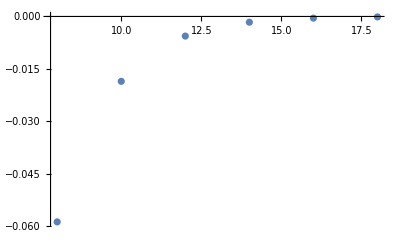

```mathematica
ListPlot[Table[{L,op[1.,L]},{L,8,18,2}]]
```

```mathematica
ListPlot[Table[{L,op[1.,L]},{L,8,18,2}]]
```

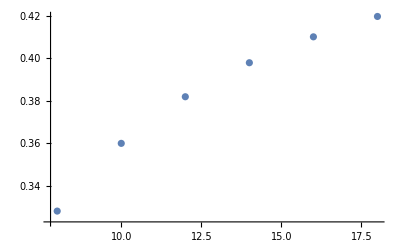

```mathematica
ListPlot[Table[{L,op[1*^-4,L]},{L,8,18,2}]]
```

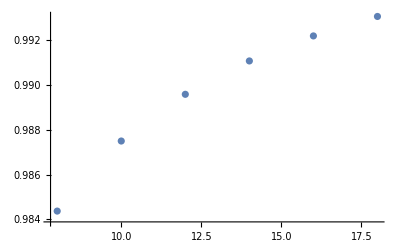

```mathematica
ListPlot[Table[{L,op[-5.,L]},{L,8,18,2}]]
```

```mathematica
Binomial[5,3]
```

10

# FM

```mathematica
op[k_,L_]:=(1-2^k)/(1-2^(k (L+1)))*(1+(1/L)*Sum[2^((k-1)F+1)*Sum[Binomial[F-1,i]*(L-2-2i),{i,0,F-1}],{F,1,L}])
```

```mathematica
op2[k_,L_]:=(1-2^k)/(1-2^(k (L+1)))*(1-(1/L)*((2^k((-2+2^k)(-1+2^(k L))+(-1+2^k)L))/((2^k-1)^2)))
```

```mathematica
op[1,#]&/@{2,4,6,8,10,12,14,16}
```

{-1/7,-1/31,-1/127,-1/511,-1/2047,-1/8191,-1/32767,-1/131071}

```mathematica
op2[1,#]&/@{2,4,6,8,10,12,14,16}
```

{-1/7,-1/31,-1/127,-1/511,-1/2047,-1/8191,-1/32767,-1/131071}

# Limit s=0

```mathematica
Limit[(2^s-1)/(2^(s L)-1),s->0]
```

1/L

```mathematica
Sum[Binomial[2n-1,2m-1]*(L-2-2*(2m-1)),{m,1,n}]
```

-4^(-1+n) (1-L+2 n)

```mathematica
FullSimplify[(√π * Gamma[2x])/(Gamma[x+1/2]*Gamma[x]),Assumptions->x∈Integers&x>0]
```

2^(-1+2 x)

```mathematica
FullSimplify[(√π * Gamma[2x-1])/(Gamma[x+1/2]*Gamma[x])*((2x)!)/((2x-2)!)*1/4,Assumptions->x∈Integers&x>0]
```

4^(-1+x) x

```mathematica
FullSimplify[(√π * Gamma[2x+1]*(2x+1))/(2*Gamma[x+3/2]*Gamma[x+1]),Assumptions->x∈Integers&x>0]
```

4^x

```mathematica
FullSimplify[(√π * Gamma[2x])/(Gamma[x+3/2]*Gamma[x+1])*((2x+1)!)/((2x-2)!)*1/8,Assumptions->x∈Integers&x>0]
```

4^(-1+x) (-1+2 x)

```mathematica
(L-4)+Sum[(L-2-k),{k,2,L-1}]//Simplify
```

1/2 (2-5 L+L^2)

```mathematica
1/L(1+1/L 1/2 (2-5 L+L^2))/.L->20.
```

0.4275

```mathematica
1/L(1+1/L 1/2 (2-5 L+L^2))//FullSimplify
```

((-2+L) (-1+L))/(2 L^2)

```mathematica
((-2+L) (-1+L))/(2 L^2)//Expand
```

1/2+1/L^2-3/(2 L)

```mathematica
(L-4)*2^s+Sum[(L-2-k)*2^(s k),{k,2,L-1}]//FullSimplify
```

-((-2+2^s) (2^(L s)+2^s (-2+2^s))+2^s (-1+2^s) L)/((-1+2^s)^2)

```mathematica
1/L *((L-4)*2^s+Sum[(L-2-k)*2^(s k),{k,2,L-1}])//FullSimplify
```

-((-2+2^s) (2^(L s)+2^s (-2+2^s))+2^s (-1+2^s) L)/((-1+2^s)^2 L)

```mathematica
(1-2^s)/(1-2^(s L))* ((-((-2+2^s) (2^(L s)+2^s (-2+2^s)))+L-2^s L)/((-1+2^s)^2 L))
```

((1-2^s) (-((-2+2^s) (2^(L s)+2^s (-2+2^s)))+L-2^s L))/((-1+2^s)^2 (1-2^(L s)) L)

```mathematica
/.{s->-0.5,L->20}
```